```mathematica
Manipulate[
{Plot[PDF[NormalDistribution[γhat, √(σγ^2/(2dγ))],x],{x,-10,10},PlotRange->All],Integrate[PDF[NormalDistribution[γhat, √(σγ^2/(2dγ))],x],{x,-∞,0}],γhat, √(σγ^2/(2dγ))},
{γhat,0.1,10,0.1},{σγ,0.1,10,0.1},{dγ,0.1,10,0.1}]
```

General::munfl: Exp[-4320.] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
n = 1000;
samples=Table[Sin[2π ii/n],{ii,0,n-1}];
FindDistribution[samples]
```

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

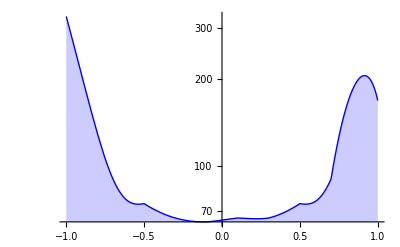

```mathematica
histogram=Histogram[samples];
datafromrectangles=Cases[histogram,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]]},All];
intF=Interpolation[datafromrectangles];

LogPlot[intF[x],{x,-1,1},PlotStyle->Directive[Blue,Thick],Filling->Axis,PlotRange->All]
```

```mathematica
Kurtosis[NormalDistribution[0,1]]
```

3

```mathematica
nsamples = 100;
samples =Table[RandomVariate[NormalDistribution[0,1]],{i,1,nsamples}];
Kurtosis[samples]
fatpdf = ProbabilityDistribution[1/(√(2π))√(ⅇ^(-x^2)),{x,-∞,∞}];
samples =Table[RandomVariate[fatpdf],{i,1,nsamples}];
Kurtosis[samples]
```

3.1712

2.7267

```mathematica
fatpdf
```

ProbabilityDistribution[(√(ⅇ^(-x^2)))/(√(2 π)),{x,-∞,∞}]

```mathematica
fatnorm = Integrate[√(ⅇ^(-x^2)),{x,-∞,∞}]
norm = Integrate[ⅇ^(-x^2),{x,-∞,∞}]
skinnorm = Integrate[ⅇ^(-x^4),{x,-∞,∞}]
```

√(2 π)

√π

2 Gamma[5/4]

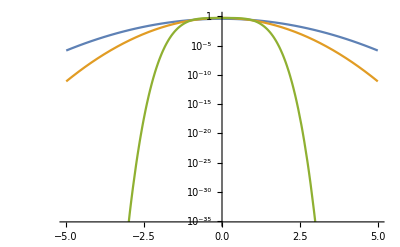

```mathematica
LogPlot[{1/fatnorm √(ⅇ^(-x^2)),1/norm ⅇ^(-x^2),1/skinnorm ⅇ^(-x^4)},{x,-5,5}]
```

```mathematica
A = {{-2γ,0,-2ω},{0,-2γ,2ω},{ω,-ω,-2γ}};
```

```mathematica
DSolve[{x'[t]==-2γ x'[t]-2ω z'[t],y'[t]==-2γ y'[t]+2ω z'[t],z'[t]==-2γ z[t] + ω(x[t] - y[t]),x[0] == x0, y[0] == y0, z[0] == z0},{x,y,z},t]
```

```mathematica
FullSimplify[{{x->Function[{t},(ⅇ^(-(2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) (ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) x0 γ+2 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) x0 γ^2-2 z0 γ ω+2 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) z0 γ ω+x0 ω^2+ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) x0 ω^2-y0 ω^2+ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) y0 ω^2))/(γ+2 γ^2+2 ω^2)],y->Function[{t},(ⅇ^(-(2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) (ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) y0 γ+2 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) y0 γ^2+2 z0 γ ω-2 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) z0 γ ω-x0 ω^2+ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) x0 ω^2+y0 ω^2+ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) y0 ω^2))/(γ+2 γ^2+2 ω^2)],z->Function[{t},(ⅇ^(-(2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) (2 z0 γ+4 z0 γ^2-x0 ω+ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) x0 ω+y0 ω-ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) y0 ω-2 x0 γ ω+2 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) x0 γ ω+2 y0 γ ω-2 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) y0 γ ω+4 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) z0 ω^2))/(2 (γ+2 γ^2+2 ω^2))]}}]
```

```mathematica
Collect[FullSimplify[(ⅇ^(-(2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) (2 z0 γ+4 z0 γ^2-x0 ω+ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) x0 ω+y0 ω-ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) y0 ω-2 x0 γ ω+2 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) x0 γ ω+2 y0 γ ω-2 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) y0 γ ω+4 ⅇ^((2 t (γ+2 γ^2+2 ω^2))/(1+2 γ)) z0 ω^2))/(2 (γ+2 γ^2+2 ω^2))],{x0,y0,z0}]
```

(x0 ((1+2 γ) ω-ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) (1+2 γ) ω))/(2 (γ+2 γ^2+2 ω^2))+(y0 ((-1-2 γ) ω+ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) (1+2 γ) ω))/(2 (γ+2 γ^2+2 ω^2))+(z0 (2 ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) γ (1+2 γ)+4 ω^2))/(2 (γ+2 γ^2+2 ω^2))

```mathematica
a[t_]:=Exp[-γ t](u10 Cos[ω t] - u20 Sin[ω t])
b[t_]:=Exp[-γ t](u20 Cos[ω t] + u10 Sin[ω t])
x[t_]:=(z0 (2 γ ω-2 ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) γ ω))/(γ+2 γ^2+2 ω^2)+(y0 (ω^2-ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) ω^2))/(γ+2 γ^2+2 ω^2)+(x0 (γ+2 γ^2+ω^2+ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) ω^2))/(γ+2 γ^2+2 ω^2)
y[t_]:=(z0 (-2 γ ω+2 ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) γ ω))/(γ+2 γ^2+2 ω^2)+(x0 (ω^2-ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) ω^2))/(γ+2 γ^2+2 ω^2)+(y0 (γ+2 γ^2+ω^2+ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) ω^2))/(γ+2 γ^2+2 ω^2)
z[t_]:=(x0 ((1+2 γ) ω-ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) (1+2 γ) ω))/(2 (γ+2 γ^2+2 ω^2))+(y0 ((-1-2 γ) ω+ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) (1+2 γ) ω))/(2 (γ+2 γ^2+2 ω^2))+(z0 (2 ⅇ^(-2 t (γ+(2 ω^2)/(1+2 γ))) γ (1+2 γ)+4 ω^2))/(2 (γ+2 γ^2+2 ω^2))
```

```mathematica
Σ[t_]:={{x[t],z[t]},{z[t],y[t]}}
u = {{u1},{u2}};
μ[t_] := {{a[t]},{b[t]}};
```

```mathematica
puγ[t_]:=Flatten[1/(2π √Det[Σ[t]])Exp[-1/2 Transpose[u-μ[t]].Inverse[Σ[t]].(u-μ[t])]][[1]]
```

```mathematica
μγ[t_]:=γhat(1 - Exp[-dγ t]) + γ0 Exp[-dγ t]
varγ[t_]:=σγ^2/(2 dγ)(1 - Exp[-2 dγ t]) + varγ0 Exp[-2 dγ t]
pγ[t_]:=1/(√(2π varγ[t]))Exp[-1/(2varγ[t])(γ-μγ[t])^2]
```

```mathematica
puγ[t_]:=ⅇ^((2 ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (γ+2 γ^2+2 ω^2) ((-u1 (u2+2 u2 γ)+u1^2 ω-u2^2 ω) (2 z0 γ+(-x0+y0) ω)+ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (u1 u2 ω (y0+2 y0 γ-x0 (1+2 γ)-4 z0 ω)+u2^2 (ω (2 z0 γ+y0 ω)+x0 (γ+2 γ^2+ω^2))+u1^2 (ω (-2 z0 γ+x0 ω)+y0 (γ+2 γ^2+ω^2)))-(-(u1+u2+2 u1 γ+2 u2 γ-2 u1 ω+2 u2 ω) (2 z0 γ+(-x0+y0) ω)+ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (u1 (4 y0 γ^2+2 y0 γ (1+ω)-4 z0 ω (γ+ω)+y0 ω (1+2 ω)+x0 ω (-1-2 γ+2 ω))+u2 (ω (y0+2 y0 γ+4 z0 γ+2 y0 ω-4 z0 ω)+x0 (4 γ^2-2 γ (-1+ω)+ω (-1+2 ω))))) {{μ1},{μ2}}[t]+(-(1+2 γ) (2 z0 γ+(-x0+y0) ω)+ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (-4 z0 ω^2+y0 (γ+2 γ^2+ω+2 γ ω+2 ω^2)+x0 (γ+2 γ^2-2 γ ω+ω (-1+2 ω)))) ({{μ1},{μ2}}[t])^2))/((2 z0 γ+(-x0+y0) ω)^2 (1+4 γ+4 γ^2+4 ω^2)-2 ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) ω (-8 z0^2 γ ω+x0^2 (ω+2 γ ω)+y0^2 (ω+2 γ ω)+2 y0 z0 (γ+2 γ^2-2 ω^2)-2 x0 (y0 (1+2 γ) ω+z0 (γ+2 γ^2-2 ω^2)))-ⅇ^(4 t (γ+(2 ω^2)/(1+2 γ))) (x0^2 ω^2 (-1+4 γ^2+4 ω^2)+ω (8 y0 z0 (1+2 γ) (γ^2+ω^2)-16 z0^2 ω (γ^2+ω^2)+y0^2 ω (-1+4 γ^2+4 ω^2))+2 x0 (-4 z0 (1+2 γ) ω (γ^2+ω^2)+y0 (8 γ^3+8 γ^4+ω^2+8 γ ω^2+4 ω^4+2 γ^2 (1+6 ω^2))))))/(π √(1/((γ+2 γ^2+2 ω^2)^2)ⅇ^(-4 t (γ+(2 ω^2)/(1+2 γ))) (-(2 z0 γ+(-x0+y0) ω)^2 (1+4 γ+4 γ^2+4 ω^2)+2 ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) ω (-8 z0^2 γ ω+x0^2 (ω+2 γ ω)+y0^2 (ω+2 γ ω)+2 y0 z0 (γ+2 γ^2-2 ω^2)-2 x0 (y0 (1+2 γ) ω+z0 (γ+2 γ^2-2 ω^2)))+ⅇ^(4 t (γ+(2 ω^2)/(1+2 γ))) (x0^2 ω^2 (-1+4 γ^2+4 ω^2)+ω (8 y0 z0 (1+2 γ) (γ^2+ω^2)-16 z0^2 ω (γ^2+ω^2)+y0^2 ω (-1+4 γ^2+4 ω^2))+2 x0 (-4 z0 (1+2 γ) ω (γ^2+ω^2)+y0 (8 γ^3+8 γ^4+ω^2+8 γ ω^2+4 ω^4+2 γ^2 (1+6 ω^2)))))))
```

```mathematica
Simplify[puγ[t]*pγ[t]]
```

```mathematica
NIntegrate[ⅇ^(-(dγ (-γ0+ⅇ^(dγ t) (γ-γhat)+γhat)^2)/(2 dγ varγ0+(-1+ⅇ^(2 dγ t)) σγ^2)+(2 ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (γ+2 γ^2+2 ω^2) ((-u1 (u2+2 u2 γ)+u1^2 ω-u2^2 ω) (2 z0 γ+(-x0+y0) ω)+ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (u1 u2 ω (y0+2 y0 γ-x0 (1+2 γ)-4 z0 ω)+u2^2 (ω (2 z0 γ+y0 ω)+x0 (γ+2 γ^2+ω^2))+u1^2 (ω (-2 z0 γ+x0 ω)+y0 (γ+2 γ^2+ω^2)))-(-(u1+u2+2 u1 γ+2 u2 γ-2 u1 ω+2 u2 ω) (2 z0 γ+(-x0+y0) ω)+ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (u1 (4 y0 γ^2+2 y0 γ (1+ω)-4 z0 ω (γ+ω)+y0 ω (1+2 ω)+x0 ω (-1-2 γ+2 ω))+u2 (ω (y0+2 y0 γ+4 z0 γ+2 y0 ω-4 z0 ω)+x0 (4 γ^2-2 γ (-1+ω)+ω (-1+2 ω))))) {{μ1},{μ2}}[t]+(-(1+2 γ) (2 z0 γ+(-x0+y0) ω)+ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (-4 z0 ω^2+y0 (γ+2 γ^2+ω+2 γ ω+2 ω^2)+x0 (γ+2 γ^2-2 γ ω+ω (-1+2 ω)))) ({{μ1},{μ2}}[t])^2))/((2 z0 γ+(-x0+y0) ω)^2 (1+4 γ+4 γ^2+4 ω^2)-2 ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) ω (-8 z0^2 γ ω+x0^2 (ω+2 γ ω)+y0^2 (ω+2 γ ω)+2 y0 z0 (γ+2 γ^2-2 ω^2)-2 x0 (y0 (1+2 γ) ω+z0 (γ+2 γ^2-2 ω^2)))-ⅇ^(4 t (γ+(2 ω^2)/(1+2 γ))) (x0^2 ω^2 (-1+4 γ^2+4 ω^2)+ω (8 y0 z0 (1+2 γ) (γ^2+ω^2)-16 z0^2 ω (γ^2+ω^2)+y0^2 ω (-1+4 γ^2+4 ω^2))+2 x0 (-4 z0 (1+2 γ) ω (γ^2+ω^2)+y0 (8 γ^3+8 γ^4+ω^2+8 γ ω^2+4 ω^4+2 γ^2 (1+6 ω^2))))))/(π^(3/2) √((ⅇ^(-2 dγ t) (2 dγ varγ0+(-1+ⅇ^(2 dγ t)) σγ^2))/dγ) √(1/((γ+2 γ^2+2 ω^2)^2)ⅇ^(-4 t (γ+(2 ω^2)/(1+2 γ))) (-(2 z0 γ+(-x0+y0) ω)^2 (1+4 γ+4 γ^2+4 ω^2)+2 ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) ω (-8 z0^2 γ ω+x0^2 (ω+2 γ ω)+y0^2 (ω+2 γ ω)+2 y0 z0 (γ+2 γ^2-2 ω^2)-2 x0 (y0 (1+2 γ) ω+z0 (γ+2 γ^2-2 ω^2)))+ⅇ^(4 t (γ+(2 ω^2)/(1+2 γ))) (x0^2 ω^2 (-1+4 γ^2+4 ω^2)+ω (8 y0 z0 (1+2 γ) (γ^2+ω^2)-16 z0^2 ω (γ^2+ω^2)+y0^2 ω (-1+4 γ^2+4 ω^2))+2 x0 (-4 z0 (1+2 γ) ω (γ^2+ω^2)+y0 (8 γ^3+8 γ^4+ω^2+8 γ ω^2+4 ω^4+2 γ^2 (1+6 ω^2))))))),{γ,-1,1}]
```

NIntegrate::inumr: The integrand (ⅇ^(-(dγ (-γ0+Power[«2»] Plus[«2»]+γhat)^2)/(2 dγ varγ0+Plus[«2»] Power[«2»])+(2 ⅇ^(2 t (γ+Times[«3»])) (γ+2 γ^2+2 ω^2) («1»))/(Power[«2»] Plus[«4»]-2 Power[«2»] ω Plus[«5»]-Power[«2»] Plus[«3»])))/(π^(3/2) √((ⅇ^(-2 dγ t) (2 dγ varγ0+(-1+ⅇ^Times[«3»]) σγ^2))/dγ) √((ⅇ^(-4 t (γ+2 Power[«2»] Power[«2»])) (-(Times[«3»]+Times[«2»])^2 (1+4 γ+4 Power[«2»]+4 Power[«2»])+«1»+ⅇ^(4 t Plus[«2»]) (Power[«2»] Power[«2»] Plus[«3»]+ω Plus[«3»]+2 x0 Plus[«2»])))/((γ+2 γ^2+2 ω^2)^2))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1}}.

NIntegrate[ⅇ^(-(dγ (-γ0+ⅇ^(dγ t) (γ-γhat)+γhat)^2)/(2 dγ varγ0+(-1+ⅇ^(2 dγ t)) σγ^2)+(2 ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (γ+2 γ^2+2 ω^2) ((-u1 (u2+2 u2 γ)+u1^2 ω-u2^2 ω) (2 z0 γ+(-x0+y0) ω)+ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (u1 u2 ω (y0+2 y0 γ-x0 (1+2 γ)-4 z0 ω)+u2^2 (ω (2 z0 γ+y0 ω)+x0 (γ+2 γ^2+ω^2))+u1^2 (ω (-2 z0 γ+x0 ω)+y0 (γ+2 γ^2+ω^2)))-(-(u1+u2+2 u1 γ+2 u2 γ-2 u1 ω+2 u2 ω) (2 z0 γ+(-x0+y0) ω)+ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (u1 (4 y0 γ^2+2 y0 γ (1+ω)-4 z0 ω (γ+ω)+y0 ω (1+2 ω)+x0 ω (-1-2 γ+2 ω))+u2 (ω (y0+2 y0 γ+4 z0 γ+2 y0 ω-4 z0 ω)+x0 (4 γ^2-2 γ (-1+ω)+ω (-1+2 ω))))) {{μ1},{μ2}}[t]+(-(1+2 γ) (2 z0 γ+(-x0+y0) ω)+ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) (-4 z0 ω^2+y0 (γ+2 γ^2+ω+2 γ ω+2 ω^2)+x0 (γ+2 γ^2-2 γ ω+ω (-1+2 ω)))) ({{μ1},{μ2}}[t])^2))/((2 z0 γ+(-x0+y0) ω)^2 (1+4 γ+4 γ^2+4 ω^2)-2 ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) ω (-8 z0^2 γ ω+x0^2 (ω+2 γ ω)+y0^2 (ω+2 γ ω)+2 y0 z0 (γ+2 γ^2-2 ω^2)-2 x0 (y0 (1+2 γ) ω+z0 (γ+2 γ^2-2 ω^2)))-ⅇ^(4 t (γ+(2 ω^2)/(1+2 γ))) (x0^2 ω^2 (-1+4 γ^2+4 ω^2)+ω (8 y0 z0 (1+2 γ) (γ^2+ω^2)-16 z0^2 ω (γ^2+ω^2)+y0^2 ω (-1+4 γ^2+4 ω^2))+2 x0 (-4 z0 (1+2 γ) ω (γ^2+ω^2)+y0 (8 γ^3+8 γ^4+ω^2+8 γ ω^2+4 ω^4+2 γ^2 (1+6 ω^2))))))/(π^(3/2) √((ⅇ^(-2 dγ t) (2 dγ varγ0+(-1+ⅇ^(2 dγ t)) σγ^2))/dγ) √(1/((γ+2 γ^2+2 ω^2)^2)ⅇ^(-4 t (γ+(2 ω^2)/(1+2 γ))) (-(2 z0 γ+(-x0+y0) ω)^2 (1+4 γ+4 γ^2+4 ω^2)+2 ⅇ^(2 t (γ+(2 ω^2)/(1+2 γ))) ω (-8 z0^2 γ ω+x0^2 (ω+2 γ ω)+y0^2 (ω+2 γ ω)+2 y0 z0 (γ+2 γ^2-2 ω^2)-2 x0 (y0 (1+2 γ) ω+z0 (γ+2 γ^2-2 ω^2)))+ⅇ^(4 t (γ+(2 ω^2)/(1+2 γ))) (x0^2 ω^2 (-1+4 γ^2+4 ω^2)+ω (8 y0 z0 (1+2 γ) (γ^2+ω^2)-16 z0^2 ω (γ^2+ω^2)+y0^2 ω (-1+4 γ^2+4 ω^2))+2 x0 (-4 z0 (1+2 γ) ω (γ^2+ω^2)+y0 (8 γ^3+8 γ^4+ω^2+8 γ ω^2+4 ω^4+2 γ^2 (1+6 ω^2))))))),{γ,-1,1}]